# Unitarity from X^a and π^a scattering.

```mathematica
(*NOTE! These formulae are all rescaled to HOPEFULLY correctly average over incoming & outgoing particle species properly. I'm not 1000% sure this is correct right now, but the results seem reasonable which is promising. However, just FYI many Feynman rules are rescaled by factors of (F^2-1).*)
```

## Formulae from 1805.07306 .

```mathematica
(*Definitions from 1805.07306*)
λ[s_,mi2_, mj2_]:=1/s^2(s^2+mi2^2+mj2^2-2mi2 mj2 -2 s mi2 -2s mj2)(*eq.7*)
modp[s_,mi2_,mj2_]:=1/2 √(s*λ[s,mi2,mj2]) (*eq.8*)
Ei[s_,mi2_,mj2_]:=(s+mi2-mj2)/(2 √s) (*eq.8*)
ft[s_,m12_,m22_,m32_,m42_,m52_]:=1/s 1/(λ[s,m12,m22]*λ[s,m32,m42])^(1/4)Log[(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]+2modp[s,m12,m22]*modp[s,m32,m42])/(m12+m32-m52-2Ei[s,m12,m22]*Ei[s,m32,m42]-2modp[s,m12,m22]*modp[s,m32,m42])](*eq. 9*)
fu[s_,m12_,m22_,m32_,m42_,m52_]:=ft[s,m12,m22,m42,m32,m52](*eq. 9*)

a0[s_]:=-2^(1/2(delta12+delta34))/(16 π)((λ[s,m12,m22]*λ[s,m32,m42])^(1/4)(-λ1234+(κ125*κ345)/(s-m52s))-κ135*κ245 *ft[s,m12,m22,m32,m42,m52t]-κ145*κ235*fu[s,m12,m22,m32,m42,m52u])(*eq. 10*)
```

## Unitarity Bound Plots in Symmetric Phase.

### Test Points (PUT THE ONE YOU WANT TO SEE LAST!) :

```mathematica
(*Van der Woude*)
(*Point B*)tVdW ={mσ2->400^2,mη2->672^2,m2->4848,λσ->25.5,λa->15.2,c->4091, F->3,p->1,fpi->90*√(3/2),Tn->145.3,Tc->145.8};
(*Point C*)tVdW={mσ2->291^2,mη2->328^2,m2->24371,λσ->14.8,λa->14.0,c->1196.,F->3,p->1,fpi->74*√(3/2),Tn->99.9,Tc->100.5};
```

```mathematica
(*Ours*)
tO= {mσ2->170000.,mη2->100.,m2->85016.66666666670,λσ->0.17,λa->3.24,c->10^-10, F->6,p->1,fpi->1000.,Tn->250,Tc->288};
tO={mσ2->90000.,mη2->100.,m2->45016.66666666700,λσ->0.09,λa->1.75,c->10^-10,F->6,p->1,fpi->1000.,Tn->195.,Tc->240.}; (*THIS POINT HAS BEST UNITARY BEHAVIOUR*)
tO={mσ2->210000.,mη2->2950.,m2->105491.66666666700,λσ->0.212,λa->3.24,c->2.95*10^-9,F->6,p->1,fpi->1000.,Tn->271.,Tc->303.};
```

### Couplings:

```mathematica
SymPhase=
{λσσXX->(λσ+2λa)+ c/F^2(p F)(p F-2)(p F-3)KroneckerDelta[p F,4],
λσσππ->λσ- c/F^2(p F)(p F-3)(p F-2)KroneckerDelta[p F,4],
ληηXX->λσ- c/F^2(p F)(p F-3)(p F-2)KroneckerDelta[p F,4],
ληηππ->(λσ+2λa)+ c/F^2(p F)(p F-3)(p F-2)KroneckerDelta[p F,4],
λXXXX->λσ+λa*(F^2-4)/(F^2-1)+c/F^2(pF)(p F^3-4 F^2+p F+6)/(F^2-1)KroneckerDelta[p F,4],
λXXππ->λσ+λa*F^2/(F^2-1)-c/F^2(pF)(p F^3- 4 F^2+p F+6)/(F^2-1)KroneckerDelta[p F,4],
λππππ->λσ+λa*(F^2-4)/(F^2-1)+c/F^2(pF)(p F^3-4 F^2+p F+6)/(F^2-1)KroneckerDelta[p F,4],
κσσσ->-c/F^2(p F)(p F-1)(p F-2)KroneckerDelta[p F,3],
κσηη->+c/F^2(p F)(p F-1)(p F-2)KroneckerDelta[p F,3],
κσXX->+c/F^2(p F)(p F-2)KroneckerDelta[p F,3],
κηXπ->-c/F^2(p F)(p F-2)KroneckerDelta[p F,3],
κσππ->-c/F^2(p F)(p F-2)KroneckerDelta[p F,3],
κXXX->-c/F^2(p F)√((F^2-4)/(F^2-1))KroneckerDelta[p F,3],
κXππ->+c/F^2(p F)√((F^2-4)/(F^2-1))KroneckerDelta[p F,3]
};
```

### Scattering σ X^a -> σ X^a :

```mathematica
(*NB should be the same as ηπ^a->ηπ^a*)
```

```mathematica
ME={λ1234 -> λσσXX,
κ125 -> κσXX,
κ345 -> κσXX,
κ135 -> κσσσ,
κ245 -> κσXX,
κ145 -> κσXX,
κ235 -> κσXX,
delta12 -> 1,
delta34 -> 1,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 -> m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

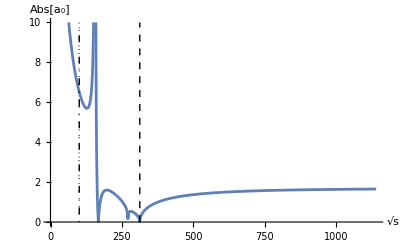

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,10},
		Epilog->{Dashed,Line[{{2 √m52s/.ME/.tVdW,0},{2 √m52s/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

```mathematica
(*Technical Minimum kinematically accessible s:*)
minrs=2 √m2/.ME/.tVdW//N
```

312.224

#### Ours

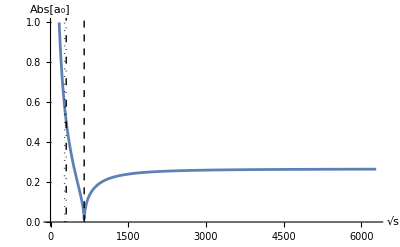

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tO]],{rootS,0,2π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{Dashed,Line[{{2 √m52s/.ME/.tO,0},{2 √m52s/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tO,0},{Tc/.tO,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

### Scattering η X^a -> η X^a:

```mathematica
(*NB should be the same as σπ^a->σπ^a*)
```

```mathematica
ME={λ1234 -> ληηXX,
κ125 -> κηXπ,
κ345 -> κηXπ,
κ135 -> κσηη,
κ245 -> κσXX,
κ145 -> κηXπ,
κ235 -> κηXπ,
delta12 -> 1,
delta34 -> 1,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 -> m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

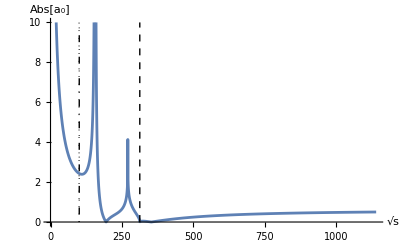

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,10},
		Epilog->{Dashed,Line[{{2 √m52s/.ME/.tVdW,0},{2 √m52s/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

```mathematica
minrs=2 √m2/.ME/.tVdW//N
```

312.224

#### Ours

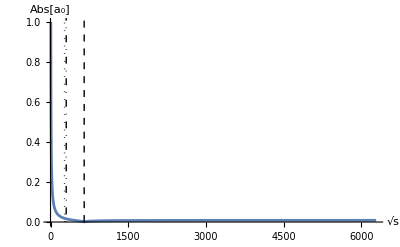

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tO]],{rootS,0,2π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{Dashed,Line[{{2 √m52s/.ME/.tO,0},{2 √m52s/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tO,0},{Tc/.tO,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

```mathematica
(*No t-pole so Technical Minimum kinematically accessible s:*)
minrs=2 √m2/.ME/.tO
```

649.59

### Scattering X^a X^b -> X^a X^b:

```mathematica
(*NOTE TO FUTURE SELF! THIS TRICK ONLY WORKS WHEN ALL PARTICLES HAVE THE SAME MASS*)
(*Also should be the same as π^a π^b->π^a π^b*)
```

```mathematica
ME={λ1234 -> λXXXX,
κ125*κ345 -> κXXX*κXXX+κσXX*κσXX,
κ135*κ245-> κσXX*κσXX,
κ145*κ235-> κXXX*κXXX+κσXX*κσXX,
delta12 -> 1,
delta34 -> 1,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 -> m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

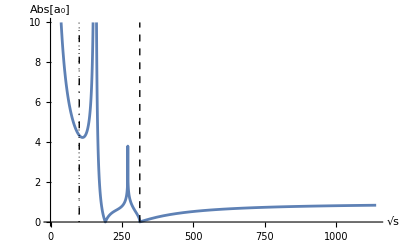

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]//.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,10},
		Epilog->{Dashed,Line[{{2 √m52s/.ME/.tVdW,0},{2 √m52s/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

```mathematica
minrs=2 √m2/.ME/.tVdW//N
```

312.224

#### Ours

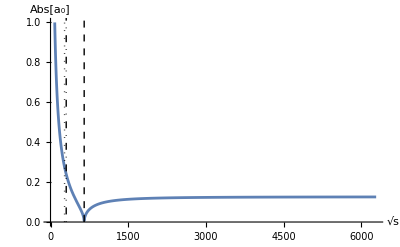

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]/.ME/.SymPhase/.tO]],{rootS,0,2π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{Dashed,Line[{{2 √m52s/.ME/.tO,0},{2 √m52s/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tO,0},{Tc/.tO,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```

### Scattering X^a π^b -> X^a π^b:

```mathematica
ME={λ1234 -> λXXππ,
κ125*κ345 -> κXππ*κXππ+κηXπ*κηXπ,
κ135*κ245-> κσXX*κσππ,
κ145*κ235->κXππ*κXππ+κηXπ*κηXπ,
delta12 -> 1,
delta34 -> 1,
m12 -> m2,(*The mass of the scattering particle I believe is m^2 in restored phase*)
m22 ->m2,
m32 -> m2,
m42 ->m2,
m52u->m2,
m52t->m2,
m52s->m2};
```

#### Van der Woude

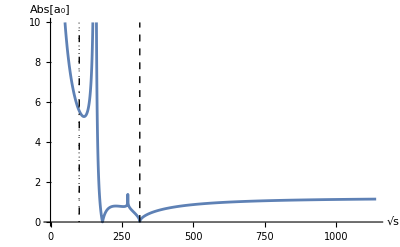

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]//.ME/.SymPhase/.tVdW]],
		{rootS,0,4*π*fpi/.tVdW},
		AxesLabel->{√s,Abs[Subscript[a, 0]]},
		PlotRange->{0,10},
		Epilog->{Dashed,Line[{{2 √m52s/.ME/.tVdW,0},{2 √m52s/.ME/.tVdW,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tVdW,0},{Tn/.tVdW,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tVdW,0},{Tc/.tVdW,10}}] (*DotDashed Vertical line indicating critical temperature*)
 }]
```

#### Ours

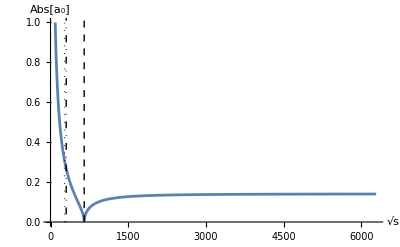

```mathematica
(*PLOT*)
Plot[Abs[Re[a0[rootS^2]//.ME/.SymPhase/.tO]],{rootS,0,2π*fpi/.tO},AxesLabel->{√s,Abs[Subscript[a, 0]]},PlotRange->{0,1},
Epilog->{Dashed,Line[{{2 √m52s/.ME/.tO,0},{2 √m52s/.ME/.tO,10}}],(*Vertical line indicating minimum Kinematically allowed √s*)
	Dotted,Line[{{Tn/.tO,0},{Tn/.tO,10}}],(*Vertical line indicating nucleation temperature*)
	DotDashed, Line[{{Tc/.tO,0},{Tc/.tO,10}}] (*DotDashed Vertical line indicating critical temperature*)}]
```